## QCD Parameters

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

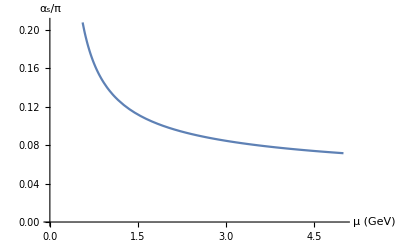

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

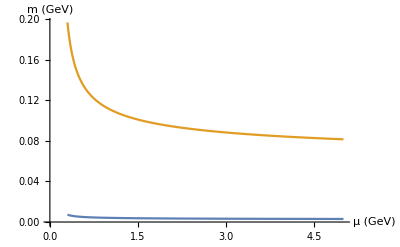

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=8.2 αGG
```

0.615

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,s,τ,s0,channel,type,terms]
```

## Procedure (Central Values)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed

## QCD Parameters + 4D Gluon Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075+0.02;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=8.2 αGG
```

0.779

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,s,τ,s0,channel,type,terms]
```

## Procedure (4D Condensate Upper Bound)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::nrnum: The function value -gaussian[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {s,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed

## QCD Parameters - 4D Gluon Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075-0.02;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=8.2 αGG
```

0.451

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,s,τ,s0,channel,type,terms]
```

## Procedure (4D Condensate Lower Bound)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::nrnum: The function value -gaussian[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {s,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed

## QCD Parameters + 6D Gluon Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2+1) αGG
```

0.69

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,s,τ,s0,channel,type,terms]
```

## Procedure (6d Condensate upper bound)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::nrnum: The function value -gaussian[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {s,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed

## QCD Parameters - 6D Gluon Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2-1) αGG
```

0.54

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,s,τ,s0,channel,type,terms]
```

## Procedure (6D Condensate lower bound)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::nrnum: The function value -gaussian[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {s,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed

## QCD Parameters + 3D Quark Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)+0.0035}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)+0.0042}
```

-0.0000892155

-0.00160179

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2) αGG
```

0.615

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,s,τ,s0,channel,type,terms]
```

## Procedure (3d condensate upper bound)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::nrnum: The function value -gaussian[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {s,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed

## QCD Parameters - 3D Quark Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)-0.0035}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)-0.0042}
```

-0.0000766423

-0.00137567

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√0.8
```

0.894427

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.6 qq

1.6 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2-1) αGG
```

0.54

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,τ,s0,channel,type,terms]/moment0[0,τ,s0,channel,type,terms]
```

## Procedure (3D condensate lower bound)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::nrnum: The function value -gaussian[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {s,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed

## QCD Parameters + 5D Mixed Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√(0.8+0.1)
```

0.948683

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.8 qq

1.8 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2) αGG
```

0.615

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,s,τ,s0,channel,type,terms]
```

## Procedure (5D condensate upper bound)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::nrnum: The function value -gaussian[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {s,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed

## QCD Parameters - 5D Mixed Condensate Error

### Running Coupling

From [1], we use the one-loop, MS-bar running coupling corresponding to four active flavors.  We take as our boundary condition α_s[M_τ]=0.326.

In the definition of α_s given, μ is in GeV.

```mathematica
Clear[α]
α[μ_]=Module[{Mτ=1.77686,ατ=0.326,nf=4,b0},
b0=1/(12π)(33-2nf);
ατ/(1+b0 ατ Log[μ^2/Mτ^2])
];
```

```mathematica
Plot[α[μ]/π,{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","α_s/π"}]
```

-Graphics-

### Running Quark Masses

From[1], we use the one-loop, MS-bar running light and strange quark masses.

Below, μ is in GeV.

```mathematica
mq[μ_]=Module[{mqat2=0.0035},
mqat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
ms[μ_]=Module[{msat2=0.095},
msat2(α[μ]/α[2])^(12/25)
];
```

```mathematica
Plot[{mq[μ],ms[μ]},{μ,0.3,5},AxesOrigin->{0,0},AxesLabel->{"μ (GeV)","m (GeV)"}]
```

-Graphics-

### Condensates

All given numerical values are in appropriate powers of GeV.

We use PCAC relations for the 4d light and strange quark condensates:

⟨m_q q̄ q⟩=-1/2 f_π^2 m_π^2

⟨m_s s̄ s⟩=-1/2 f_K^2 m_K^2.

Meson masses are taken from [1].  The pion decay constant is from [2].  The kaon decay constant is from....

```mathematica
mqq=-0.5 Mpi^2 fpi^2/.{Mpi->0.13957018,fpi->0.1304/(√2.)}
mss=-0.5 MK^2 fK^2/.{MK->0.493677,fK->0.1562/(√2.)}
```

-0.0000828096

-0.00148658

The 4d gluon condensate value is taken from [2]:

```mathematica
αGG=0.075;
```

Let κ be the strange quark condensate scaling ratio defined by

κ=(<s̄ s>)/(<d̄ d>).

From [2], we have that

```mathematica
κ=0.74;
```

For the mixed condensate, from [2,3]

```mathematica
M0=√(0.8-0.1)
```

0.83666

```mathematica
gqGq=2 M0^2 qq
gsGs=2 M0^2 ss
```

1.4 qq

1.4 ss

It looks as if there are improvements to be made to our implementation of the mixed condensate (see [2]).

For the 6d gluon condensate, we have from [2]:

```mathematica
gggGGG=(8.2-1) αGG
```

0.54

The following values of the 6d quark condensate come from [3] where deviations from the vacuum saturation hypothesis are taken into account:

```mathematica
(*αqqqq=1.3 10^-4*) (* exact vacuum saturation *)
αqqqq=3.5 10^-4
αssss=κ^2 αqqqq
```

0.00035

0.00019166

### References

[1] Olive et al. (Particle Data Group), Chin.Phys.C38, (2014) 090001

[2] Narison, Nuclear and Particle Physics Proceedings 00 (2015) 1 [arXiv:1511.05903v3]

[3] Latorre, Pascual, Narison, Z.Phys.C34 (1987) 347

## Gaussian Sum-Rules (2017-08-02)

```mathematica
gaussian[k_,s_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG(-4α[τ^(1/4)])/π Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[((a t^3+b t^2)+(c t+d+f))t^k(1/(√(4π τ)))Exp[(-(t-s)^2)/(4τ)],{t,0,s0}]

];
```

```mathematica
moment0[k_,
τ_?NumericQ,
s0_?NumericQ,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG((-4α[τ^(1/4)])/π ) Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)t^k ,{t,0,s0}]

];
```

```mathematica
momentN[n_,k_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=
Module[
{a,b,c,d,e,f,αs=α[τ^(1/4)],m,mψψ,mgψσGψ,αψψψψ},
m=Switch[type,"light",mq[τ^(1/4)],"strange",ms[τ^(1/4)]];
mψψ=Switch[type,"light",mqq,"strange",mss];
mgψσGψ=Switch[type,"light",2 M0^2 mqq,"strange",2 M0^2 mss];
αψψψψ=Switch[type,"light",αqqqq,"strange",αssss];
a=terms[[1]]αs Switch[channel,"0++",-1/(480 π^3),"1-+",-1/(240 π^3),"0--",-1/(480 π^3),"1+-",-1/(240 π^3),"0-+",-1/(480 π^3),"1++",-1/(240 π^3),"0+-",-1/(480 π^3),"1--",-1/(240 π^3)];
b=terms[[2]]αs m^2 Switch[type,"light",0,"strange",Switch[channel,"0++",0,"1-+",1/(12 π^3),"0--",1/(16 π^3),"1+-",5/(48 π^3),"0-+",0,"1++",1/(12 π^3),"0+-",1/(16 π^3),"1--",5/(48 π^3)]];
c=terms[[3]]αs mψψ Switch[channel,"0++",1/(3π),"1-+",-2/(9π),"0--",-1/(3π),"1+-",-4/(9π),"0-+",1/(3π),"1++",-2/(9π),"0+-",-1/(3π),"1--",-4/(9π)]+terms[[4]]αGG Switch[channel,"0++",1/(24π),"1-+",-1/(36π),"0--",1/(24π),"1+-",-1/(36π),"0-+",-1/(24π),"1++",1/(36π),"0+-",-1/(24π),"1--",1/(36π)];
d=terms[[5]]αs mgψσGψ Switch[channel,"0++",1/(9π),"1-+",0,"0--",11/(72π),"1+-",-19/(72π),"0-+",-1/(9π),"1++",0,"0+-",-11/(72π),"1--",19/(72π)];
e=terms[[6]]αψψψψ Switch[channel,"0++",(-4π)/3,"1-+",(4π)/9,"0--",(4π)/3,"1+-",(-4π)/9,"0-+",0,"1++",(-8π)/9,"0+-",0,"1--",(8π)/9];f=terms[[7]]gggGGG ((-4α[τ^(1/4)])/π )Switch[channel,"0++",-1/(192 π^2),"1-+",1/(192 π^2),"0--",-1/(192 π^2),"1+-",1/(192 π^2),"0-+",5/(192 π^2),"1++",-5/(192 π^2),"0+-",5/(192 π^2),"1--",-5/(192 π^2)];

-Integrate[(d+f+c t+b t^2+a t^3)(1/(2 √π)t^k τ^(-1/2+n/2) (-((-2)^n-2^n) t Gamma[1+n/2] Hypergeometric1F1[(1-n)/2,3/2,-t^2/(4 τ)]+((-2)^n+2^n) √τ Gamma[(1+n)/2] Hypergeometric1F1[-n/2,1/2,-t^2/(4 τ)])) ,{t,0,s0}]

];
```

```mathematica
(* Exclusively using k = 0 weight *)
σSqrd[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^2
A[τ_?NumericQ,s0_?NumericQ,channel_,type_]:=momentN[3,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type]-3(momentN[2,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])+2(momentN[1,0,τ,s0,channel,type]/moment0[0,τ,s0,channel,type])^3
```

```mathematica
(* Exclusively using k = 0 weight *)
normGaussian[s_,
τ_,
s0_,
channel_?(MemberQ[{"0++","1-+","0--","1+-","0-+","1++","0+-","1--"},#]&),
type_?(MemberQ[{"light","strange"},#]&),
terms_:Table[1,{7}]
]:=gaussian[0,s,τ,s0,channel,type,terms]/moment0[0,s,τ,s0,channel,type,terms]
```

## Procedure (5D condensate lower bound)

```mathematica
(*BEGIN PARAMETERS*)
jpcTable={"0+-", "1-+", "0++", "1--", "0--" ,"1++", "0-+", "1+-"};
flavorTable={"light","strange"};
tauList=Table[τ,{τ,2,4,0.25}];
(*s0 list using normalized chisquared*)
s0List[flavor_?StringQ]:=Piecewise[{{{2.305472667063503,1.606220841985824,7.613991604035583,9.358747341598987,7.632185829922959,9.358230286443721,2.2991049361657874,1.5975340620440377},flavor=="light"},{{2.397102853683307,1.701467016244829,7.440044465050361,9.604143585591114,5.003817327381212,9.55151974769491,2.227961192952702,1.48327020738854},flavor=="strange"}}]
(*END PARAMETERS*)

(*BEGIN FUNCTION DEFINITIONS*)
s0optimizedList[flavor_?StringQ]:=Piecewise[{{{},flavor=="light"},{{},flavor=="strange"}}]
sPeak[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindArgMax[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
peakHeight[τ_?NumericQ,s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=FindMaxValue[{normGaussian[s,τ,s0,jpc,flavor],s>0},s,MaxIterations->150]
resonanceMass[s0_?NumericQ,jpc_?StringQ,flavor_?StringQ]:=Sqrt[(1/Length[tauList])Sum[sPeak[tauList[[i]],s0,jpc,flavor],{i,1,Length[tauList]}]]
s0opt[jpc_?StringQ,flavor_?StringQ,seed_:7]:=
FindArgMin[Sum[(sPeak[tauList[[i]],s0,jpc,flavor]/resonanceMass[s0,jpc,flavor]^2-1)^2,{i,1,Length[tauList]}],{s0,seed}][[1]]
model[s_,τ_,m_]:=1/Sqrt[4τ π ] Exp[(-(s-(m)^2)^2)/(4τ)]
(*END FUNCTION DEFINITIONS*)
```

```mathematica
For[i=1,i≤Length[flavorTable],i++,
For[j=1,j≤Length[jpcTable],j++,
Clear[jpc,flavor];
flavor=flavorTable[[i]];
jpc=jpcTable[[j]];
s0optimized=s0List[flavor][[j]];

Clear[filename,input,max,massPrediction];
max=Parallelize[Table[FindMaximum[normGaussian[τ,s0optimized,jpc,flavor],{s,10}],{τ,1,25,0.25}],Method->"CoarsestGrained"];
massPrediction=TakeSmallest[Table[Sqrt[s]/.max[[i,2]],{i,1,Length[max]}],1];
filename=StringJoin[DateString["ISODate"],"-modelCompare-",ToString[flavor],"_",ToString[jpc]];
input=Prepend[Parallelize[Table[{s,Evaluate@normGaussian[2,s0optimized,jpc,flavor],model[s,2,massPrediction],Evaluate@normGaussian[3,s0optimized,jpc,flavor],model[s,3,massPrediction],Evaluate@normGaussian[4,s0optimized,jpc,flavor],model[s,4,massPrediction]},{s,-5,15,0.2}],Method->"CoarsestGrained"],{"s","Sum-rule (τ=2)","Model (τ=2)","Sum-rule (τ=3)","Model (τ=3)","Sum-rule (τ=4)","Model (τ=4)"}];
Put[filename];
PutAppend[input,filename];
Clear[filename,input,max,massPrediction];
]
]
```

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

FindMaximum::nrnum: The function value -gaussian[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}]/moment0[0,τ,s0List⟦1⟧,0+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {s,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0+-.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_1-+.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Put::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of Put::noopen will be suppressed during this calculation.

PutAppend::noopen: Cannot open 2017-09-20-modelCompare-light_0++.

General::stop: Further output of PutAppend::noopen will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,light,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦1⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦1⟧,0+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦2⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦2⟧,1-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦3⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦3⟧,0++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦4⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦4⟧,1--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦5⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦5⟧,0--,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦6⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦6⟧,1++,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦7⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦7⟧,0-+,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Part::partd: Part specification s0List⟦8⟧ is longer than depth of object.

FindMaximum::nrnum: The function value -gaussian[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.25,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,1.5,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

FindMaximum::nrnum: The function value -gaussian[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}]/moment0[0,13.75,s0List⟦8⟧,1+-,strange,{1,1,1,1,1,1,1}] is not a real number at {s} = {10.}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {-5.,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {5.2,10} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
lightSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-light.m"]
strangeSummary>>StringJoin[DateString["ISODate"],"_SumRuleErrorSummary-strange.m"]
```

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-light.m.

$Failed

Put::noopen: Cannot open 2017-09-20_SumRuleErrorSummary-strange.m.

$Failed